```mathematica
SetDirectory[NotebookDirectory[]];
sp = Import["JinData_out_haploid-gen.csv"];*)
(*sp = Import["BC_analysis.csv"]; *)
(*runningColor=Red;*)
```

```mathematica
Length[sp]
```

48

```mathematica
mupr[ν_,λ_,n_]:=2^ν Exp[-λ/2]Gamma[ν+n/2]Hypergeometric1F1Regularized[ν+n/2,n/2,λ/2]
```

```mathematica
mu[k_Integer,γ_,l_,n_,{σA_,s_}]:=
(l^2/s^2)^(k γ)Sum[Binomial[k,i](-1)^i mupr[γ i,l^2 n/σA^2,n](l^2 n/σA^2)^(-γ i),{i,0,k}]
```

```mathematica
mm1=mu[1,γ,l,n,{σA,s}];
```

```mathematica
ss2=mu[2,γ,l,n,{σA,s}]-mu[1,γ,l,n,{σA,s}]^2//Factor;
```

```mathematica
Part[FindRoot[x^2-3==0,{x,0.4}],1,2]
```

1.73205

```mathematica
(*parameters*)
dims=80;  (*dimensions*)
si=1.5;  (*stress intensity*)
gamma =3; (* speed of decay function*)
tA=0.95;(*aneuploid dispersion*)
```

```mathematica
fMS=Function[l,Evaluate[{mm1,Sqrt[ss2]}/.{n->dims,σA->tA,s->si,γ->gamma}]];
fM=Function[l,Evaluate[mm1/.{n->dims,σA->tA,s->si,γ->gamma}]];
fS=Function[l,Evaluate[Sqrt[ss2]/.{n->dims,σA->tA,s->si,γ->gamma}]];
 fl[y_]:=Part[FindRoot[fM[x]-y,{x,0.2}],1,2];
Plot[fM[l],{l,0,0.6}];
ls=Table[fl[l],{l,Transpose[sp][[1]]}];
bins = Map[fS,ls]-Transpose[sp][[2]];
bins=Map[Function[x,x^2],bins];
sm=Total[bins] (*value of interest*)
(* sm = Sum[i^2,{i,bins}] *)
SSe = StandardDeviation[Transpose[sp][[2]]]*Length[Transpose[sp][[2]]];
r2 = 1-sm/SSe
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

16.7443

0.238864

Power::infy: Infinite expression 1/0.^6 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^6 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

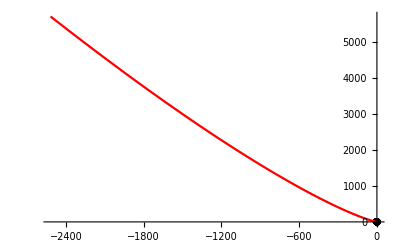

```mathematica
mem2 = Show[ListPlot[sp,
PlotRange->{{0,-2},{0,2}},
PlotStyle->Black,
 AxesOrigin->{0,0},
AxesStyle->Thick,
TicksStyle->Bold],
ParametricPlot[{fM[l],fS[l]},
{l,0.0,10},
PlotRange->{{0,-2},{0,2}},
 PlotStyle->Red]]
```

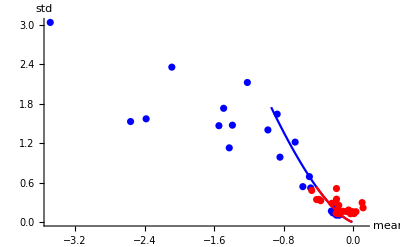

```mathematica
Show[mem1,mem2]
```